```mathematica
Quit[];
```

```mathematica
Needs["MyStyle`"]
```

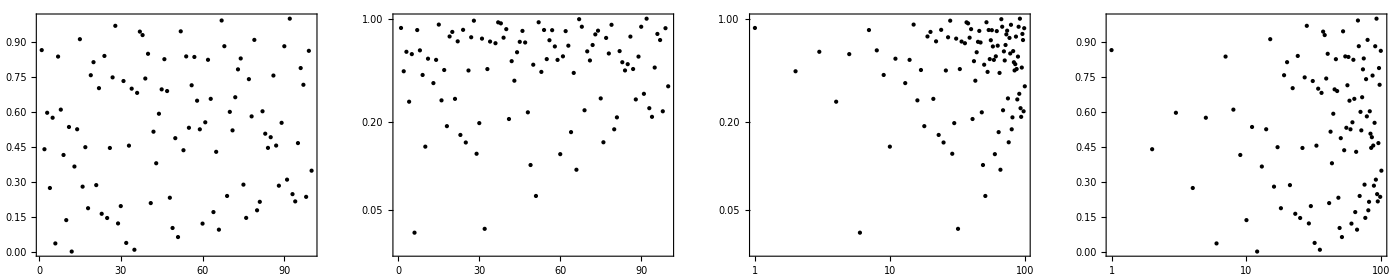

```mathematica
rndDat=RandomReal[{0,1},100];
GraphicsRow[{ListPlot[rndDat],
ListLogPlot[rndDat],
ListLogLogPlot[rndDat],
ListLogLinearPlot[rndDat]},ImageSize->4*350]
```

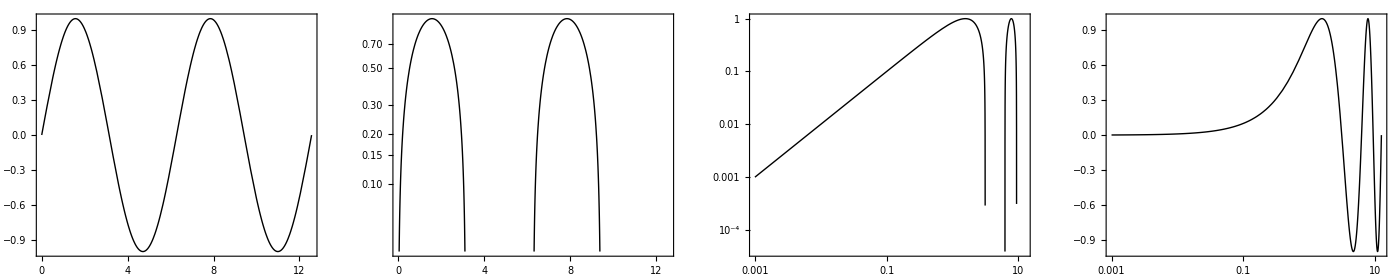

```mathematica
args=Sequence[Sin[x],{x,0.001,4Pi}];
GraphicsRow[{Plot[Evaluate[args]],
LogPlot[Evaluate[args]],
LogLogPlot[Evaluate[args]],
LogLinearPlot[Evaluate[args]]},ImageSize->4*350]
```

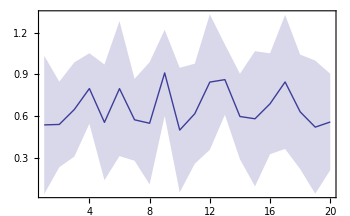

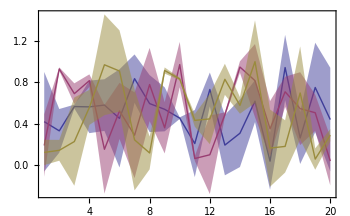

```mathematica
errorListPlotBand[RandomReal[{0.5,1},{20,2}]]
errorListPlotBand[Sequence@@RandomReal[{0,1},{3,20,2}]]
```